```mathematica
(* Method of moments estimator *)
(*Function to generate rate matrix from an edge list and weights*)RateMatrix[edges_List,weights_List,n_Integer]:=Module[{Q},Q=ConstantArray[0,{n,n}];
Do[Q[[edges[[i,1]],edges[[i,2]]]]=weights[[i]],{i,Length[edges]}];
Do[Q[[i,i]]=-Total[Q[[i,All]]],{i,n}];
Q];

(*Function to compute steady-state probabilities*)SteadyStateProbabilities[Q_]:=Module[{n,A,b,π},n=Length[Q];
A=Append[Transpose[Q],ConstantArray[1,n]];
b=Append[ConstantArray[0,n],1];
π=LinearSolve[A,b];
π];

(*Function to compute mean first passage times*)
MeanFirstPassageTimes[Q_]:=Module[{n,Z,T},n=Length[Q];
ss = SteadyStateProbabilities[Q];
Pss = Table[ss, {i,n}];
Z=Inverse[Pss-Q]-Pss;
T=Table[(Z[[j,j]]-Z[[i,j]])/ss[[j]],{i,n},{j,n}];
Simplify[T]];

MeanFirstPassageTimes2[Q_]:=Module[{n,T,subIdxs,Qsub,rhs,x},n=Length[Q];
T=ConstantArray[0,{n,n}];(*to hold T_{i->j} for i,j=1..n*)
Do[If[i==j,(*If same state,MFPT=0 by definition*)
T[[i,j]]=0,(*Else i!=j,solve the submatrix system:*)
subIdxs=Delete[Range[n],j];(*The set of states except j*)
Qsub=Q[[subIdxs,subIdxs]];(*Q^(j):remove row j,col j*)
rhs=-ConstantArray[1,n-1];(*-1 vector*)(*Solve Qsub x=-1*)
x=LinearSolve[Qsub,rhs];
(*x maps subIdxs->T_{(subIdxs)->j}.We want the entry for i.*)
T[[i,j]]=x[[First@Position[subIdxs,i]]];],{i,1,n},{j,1,n}];
Return[T];];

VarianceFirstPassageTimes[Q_]:=Module[{n,T,subIdxs,Qsub,rhs,x},n=Length[Q];
m = MeanFirstPassageTimes2[Q];
T=ConstantArray[0,{n,n}];(*to hold T_{i->j} for i,j=1..n*)
Do[If[i==j,(*If same state,MFPT=0 by definition*)
T[[i,j]]=0,(*Else i!=j,solve the submatrix system:*)
subIdxs=Delete[Range[n],j];(*The set of states except j*)
Qsub=Q[[subIdxs,subIdxs]];(*Q^(j):remove row j,col j*)
rhs=-2*m[[subIdxs,j]];(*-1 vector*)(*Solve Qsub x=-2m*)
x=LinearSolve[Qsub,rhs];
(*x maps subIdxs->T_{(subIdxs)->j}.We want the entry for i.*)
T[[i,j]]=x[[First@Position[subIdxs,i]]] - m[[i,j]]^2;],{i,1,n},{j,1,n}];
Return[T];];

LaplaceTransformFPT[Q_,s_]:=Module[{n,T,subIdxs,Qsub,rhs,x},n=Length[Q];
T=ConstantArray[0,{n,n}];
(*T[[i,j]] will store phi_{i->j}(s)=E[e^{-s T_{i->j}}].*)Do[If[i==j,(*By definition,time from j to j is 0=>Laplace transform=E[e^{-s*0}]=1*)
T[[i,j]]=1,(*i!=j:solve the submatrix system (Q+sI)_{S' x S'}*phi_{S'}=-Q_{S',j},using the boundary condition phi_j(s)=1.*)
subIdxs=Delete[Range[n],j];(*states except j*)
Qsub=Q[[subIdxs,subIdxs]]-s*IdentityMatrix[n-1];
(*Build the inhomogeneous RHS=-Q[i,j],for each i in subIdxs*)rhs=Table[-Q[[subIdxs[[row]],j]],{row,1,n-1}];
x=LinearSolve[Qsub,rhs];
(*x gives phi_{k->j}(s) for k in subIdxs.We want the component corresponding to i.*)T[[i,j]]=x[[First@Position[subIdxs,i]]];],{i,1,n},{j,1,n}];
Return[FullSimplify[T]];];

LaplaceTransformToSetByState[Q_,start_,hit_List,s_]:=Module[{n=Length[Q],subStates,m,results,eqMatrix,eqRHS,hj,sol,iPos},(*If'start' is already in'hit',then the time is 0 with prob=1=>transform=1,but specifically we don't "hit h_j first" if j!=that state.We'll handle it below.*)If[MemberQ[hit,start],(*Then we trivially return a vector of dimension Length[hit],where the entry for'start' is 1,and all others 0.*)
Return[Map[If[#==start,1,0]&,hit]]];
(*Otherwise,we solve one linear system for each h_j in'hit'.*)
subStates=Complement[Range[n],hit];(*non-absorbing set*)m=Length[subStates];
results=Table[((*Build the (Q-sI) submatrix for non-absorbing states.*)eqMatrix=Table[Q[[subStates[[i]],subStates[[j]]]],{i,m},{j,m}];
Do[eqMatrix[[i,i]]-=s,{i,1,m}];
(*RHS=-Q_{i,h_j},for each i in subStates.*)
eqRHS=Table[-Q[[subStates[[i]],hj]],{i,1,m}];
(*Solve and get phi_i^(j)(s).Then extract the'start' component.*)
sol=LinearSolve[eqMatrix,eqRHS];
iPos=First@Position[subStates,start];
sol[[iPos]]),{hj,hit}  (*for each absorbing state in'hit'*)];
Return[results];];

LogSpecificity[c_,ω_,γ_,rates_,edges_]:= Module[{n,Q, weights,ss,kboff,konb,kuon,kbon,koffu,kuoff},
{kboff,konb,kuon,kbon,koffu,kuoff} = Table[rates[[i]][[1]]/.rates[[i]],{i,1,Length[rates]}];
weights={c*kboff,kuoff,ω*c*kboff,γ*kuoff,c*kbon,kuon,ω*c*kbon,γ*kuon,konb,koffu,konb};
Q = RateMatrix[edges, weights,6];
ss = SteadyStateProbabilities[Q];
Log[ss[[3]]/ss[[5]]] + Log[ω/γ]
]
```

```mathematica
(*----------------------------------------------------------------------------------------------------------*)(*** Decoys, 2 binding sites ***)

(*Edge lists and weights*)
edges2={{5,1},{1,5},{2,6},{6,2},{1,2},{1,3},{2,4},{3,1},{3,4},{4,2},{6,5},{5,6}};
weights2={2*c*kboff,kuoff,kuon,2*c*kbon,kon1b,c*kboff,c*kbon,2*kuoff,kon2b,2*kuon,koffu,konu};
nstates2 = 6;
nedges2 = Length[edges2];
assum = c>=0&&kboff>0&&kuon>0&&kbon>0&&kon1b>0&&kuoff>0&&kon2b>0&&koffu>0;
```

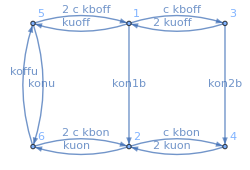

```mathematica
(*Plot the circuit*)
edgeList=Table[edges2[[i,1]]->edges2[[i,2]],{i,1,nedges2}];
g=Graph[edges2,VertexLabels->"Name",DirectedEdges->True,EdgeLabels->Table[edgeList[[i]]->Placed[(HoldForm/@weights2)[[i]],0.55],{i,1,nedges2}],ImageSize->250, GraphLayout->{"MultipartiteEmbedding","VertexPartition"->{{6,5},{2,1},{4,3}}}]
```

```mathematica
Q2 = RateMatrix[edges2, weights2, nstates2];
ss2 = SteadyStateProbabilities[Q2];
```

```mathematica
(*Laplace transform of FPTs for individual hitting states*)
Fon = LaplaceTransformFPT[Q2,s2];
F25 = Fon[[2,5]][[1]];
F45 = Fon[[4,5]][[1]];
F65 = Fon[[6,5]][[1]];
```

```mathematica
(*Laplace for hitting set, joint with the hitting state*)
offStates = {5,1,3};
onStates = {6,2,4};
F5on = LaplaceTransformToSetByState[Q2,5,onStates,s1];
FoffOn = F5on[[2]][[1]]*F25 +F5on[[3]][[1]]*F45;
```

```mathematica
(*Means, variances and covariances of FPTs from the Laplace transforms*)
partials1 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s1,1}]]];
partials2 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s2,1}]]];
partials1s1 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s1,2}]]];
partials2s2 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s2,2}]]];
partials1s2 = With[{s1=0, s2=0}, Evaluate[D[D[FoffOn, {s2,1}],{s1,1}]]];

meanToffLt = -partials1;
meanTonLt = -partials2;
varToffLt = partials1s1 - meanToffLt^2;
varTonLt = partials2s2 - meanTonLt^2;
covTonToff = partials1s2 - meanToffLt*meanTonLt;
τ = Simplify[meanToffLt + meanTonLt,assum];
```

```mathematica
(*Covariance matrix*)
Σx = Simplify[{{varToffLt,covTonToff},{covTonToff,varTonLt}},assum];
```

```mathematica
(*MM estimators*)
cHatOffSym =Simplify[c/.Solve[meanToffLt==sampleToff,c][[1]],assum];
cHatOnSym = Simplify[c/.Solve[meanTonLt==sampleTon,c][[1]],assum];
```

```mathematica
Solve[meanToffLt==sampleToff,c][[1]]
```

```mathematica
cHatOffSym
```

```mathematica
FullSimplify[With[{sampleToff=meanToffLt},Evaluate[cHatOffSym]],assum]
```

```mathematica
(*Jacobian*)
dcHatOff=With[{sampleToff=meanToffLt},Evaluate[D[cHatOffSym, {sampleToff,1}]]];
dcHatOn=With[{sampleTon=meanTonLt},Evaluate[D[cHatOnSym, {sampleTon,1}]]];
delf = {{dcHatOff,0},{0,dcHatOn }};
```

```mathematica
(*Covariance matrix of estimators*)
Σy = delfᵀ.Σx.delf;
```

```mathematica
(*Combined estimator and its variance*)
σ2off = Σy[[1,1]];
σ2on = Σy[[2,2]];
Cov = Σy[[1,2]];

cHat = (cHatOffSym*(σ2on-Cov) + cHatOnSym*(σ2off-Cov))/(σ2off + σ2on - 2Cov);
σ2 = (σ2on*σ2off - Cov^2)/(σ2off + σ2on - 2Cov);

(*Concentration-rescaled Fisher information rates*)
Foff = c^2/ (τ*σ2off);
Fon = c^2/ (τ*σ2on);
Fcomb = c^2/ (τ*σ2);
F[c_,kboff_,kuoff_,kuon_,kbon_,kon1b_,kon2b_,koffu_] := Evaluate[Fcomb];
G[c_,lnkboff_,lnkuoff_,lnkuon_,lnkbon_,lnkon1b_,lnkon2b_,lnkoffu_]:=F[c,Exp[lnkboff],Exp[lnkuoff],Exp[lnkuon],Exp[lnkbon],Exp[lnkon1b],Exp[lnkon2b],Exp[lnkoffu]]
```

```mathematica
(*Maximize*)
lnkmin = -5;
lnkmax = Log[5];
lnkdifflim = Log[0.0888];
cvals = Table[10.^x, {x,Subdivide[-2,4,15]}];
rates = Table[NMaximize[{G[c,lnkboff,lnkuoff,lnkuon,lnkbon,lnkon1b,lnkon2b,lnkoffu]/.{c->x},
lnkmin<lnkboff<lnkdifflim,
lnkmin<lnkuoff<lnkmax,
lnkmin<lnkuon<lnkmax,
lnkmin<lnkbon<lnkdifflim,
lnkmin<lnkon1b<lnkmax,
lnkmin<lnkon2b<lnkmax,
lnkmin<lnkoffu<lnkmax},
{lnkboff,lnkuoff,lnkuon,lnkbon,lnkon1b,lnkon2b,lnkoffu},
Method->"DifferentialEvolution"],{x,cvals}]
```

$Aborted

```mathematica
Test[cval_,lnrates_] := Module[{x1,x2,x3,x4,x5,x6,x7},
{x1,x2,x3,x4,x5,x6,x7} = Table[Exp[r],{r,lnrates}];
With[{c=cval,kboff=x1,kuoff=x2,kuon=x3,kbon=x4,kon1b=x5,kon2b=x6,koffu=x7},
Evaluate[τ]]];
```

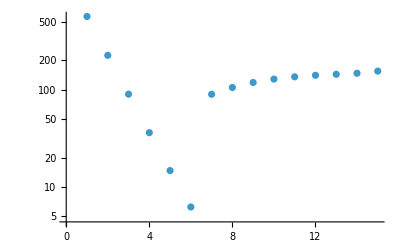

```mathematica
ListPlot[Table[Test[cvals[[k]],Table[rates[[k]][[2]][[i]][[2]],{i,1,7}]],{k,1,15}], ScalingFunctions->"Log"]
```

```mathematica
A = {{a1,0},{0,a4}};
B = {{b1,b2},{b3,b4}};
Aᵀ.B.A
```

{{a1^2 b1,a1 a4 b2},{a1 a4 b3,a4^2 b4}}